## Linearized Equation of Motion

With Snell’s Law and Left-right Symmetry

## Build Functions

```mathematica
Hamil[identifierList_]:=Module[{lenM,hamiltonianM,hvM,hvBareM,s2thetavM,c2thetavM},
(* identifierList = {
{ rho, omegav, mu, theta }
} *)
s2thetavM=0.0;
c2thetavM=√(1-s2thetavM);
lenM=Length@identifierList;

hvBareM=(-c2thetavM{{1,0},{0,-1}}+s2thetavM{{0,1},{1,0}});
hvM=Table[identifierList[[i,2]]*hvBareM/2,{i,1,lenM}];
hamiltonianM=Table[(1-Cos[ identifierList[[i,4]] - identifierList[[j,4]] ])*identifierList[[j,3]]*identifierList[[j,1]] ,{i,1,lenM},{j,1,lenM}];

hvM+Total[hamiltonianM,{2}]

]
```

```mathematica
Commutator[mat1_,mat2_]:=mat1.mat2-mat2.mat1
```

```mathematica
RHS[identifierList_,h_,variables_]:=Module[{rhsM,lenM,rhsrulesM,lsaMatM},

lenM=Length@identifierList;
rhsM=Table[2Commutator[h[[i]],identifierList[[i,1]]][[1,2]],{i,1,lenM}]//Simplify;
rhsrulesM=CoefficientRules[rhsM,variables];

lsaMatM={
{1,0,0,0}/.rhsrulesM,
{0,1,0,0}/.rhsrulesM,
{0,0,1,0}/.rhsrulesM,
{0,0,0,1}/.rhsrulesM
}//Simplify;

lsaMatM
]
```

```mathematica
IDLConstructor[th_,mu_,omegav_,variables_]:=Module[{idListM,rhoListM},

rhoListM=Table[{ { 1,variables[[i]] },{Conjugate@variables[[i]],-1} }/2,{i,1,Length@variables}];


idListM=Table[
{rhoListM[[i]],omegav[[i]],mu[[i]],th[[i]]},
{i,1,Length@variables}
];

idListM

]
```

```mathematica
MaxEV[identifierList_,variables_]:=Module[{hM,lsaMatM,maxEVM},

hM=Hamil[identifierList]//Simplify;
lsaMatM=RHS[identifierList,hM,variables];
maxEVM=Max@Im@Eigenvalues[
lsaMatM
];

maxEVM
]
```

## Test Functions

Test Hamiltonian

```mathematica
rho1Eg={{1,epsF1Eg},{Conjugate@epsF1Eg,-1}}/2
rho2Eg={{1,epsF2Eg},{Conjugate@epsF2Eg,-1}}/2
idListEg={
{rho1Eg,1,muVal,theta1},
{rho2Eg,1,R muVal,theta2}
}
hEg=Hamil[idListEg]
hEg[[1]].rho1-rho1.hEg[[1]]//Simplify//MatrixForm
```

{{1/2,epsF1Eg/2},{Conjugate[epsF1Eg]/2,-1/2}}

{{1/2,epsF2Eg/2},{Conjugate[epsF2Eg]/2,-1/2}}

{{{{1/2,epsF1Eg/2},{Conjugate[epsF1Eg]/2,-1/2}},1,muVal,theta1},{{{1/2,epsF2Eg/2},{Conjugate[epsF2Eg]/2,-1/2}},1,muVal R,theta2}}

{{{-0.5+1/2 muVal R (1-Cos[theta1-theta2]),0.+1/2 epsF2Eg muVal R (1-Cos[theta1-theta2])},{0.+1/2 muVal R Conjugate[epsF2Eg] (1-Cos[theta1-theta2]),0.5-1/2 muVal R (1-Cos[theta1-theta2])}},{{-0.5+1/2 muVal (1-Cos[theta1-theta2]),0.+1/2 epsF1Eg muVal (1-Cos[theta1-theta2])},{0.+1/2 muVal Conjugate[epsF1Eg] (1-Cos[theta1-theta2]),0.5-1/2 muVal (1-Cos[theta1-theta2])}}}

-rho1.{{-0.5+0.5 muVal R-0.5 muVal R Cos[theta1-theta2],-1/2 epsF2Eg muVal R (-1+Cos[theta1-theta2])},{-1/2 muVal R Conjugate[epsF2Eg] (-1+Cos[theta1-theta2]),0.5-0.5 muVal R+0.5 muVal R Cos[theta1-theta2]}}+{{-0.5+0.5 muVal R-0.5 muVal R Cos[theta1-theta2],-1/2 epsF2Eg muVal R (-1+Cos[theta1-theta2])},{-1/2 muVal R Conjugate[epsF2Eg] (-1+Cos[theta1-theta2]),0.5-0.5 muVal R+0.5 muVal R Cos[theta1-theta2]}}.rho1

Hamiltonian test pass!

Unit Test for  Commutator

```mathematica
Commutator[PauliMatrix[1],PauliMatrix[2]]-2I PauliMatrix[3]
(* Should return 0 matrix *)
```

{{0,0},{0,0}}

## Build Identity List

The identities should be of the form
identifierList = {
{ rho1, omegav1, mu1, theta1 },
{ rho2, omegav2, mu2, theta2 }
}

```mathematica
varList={epsF1,epsF2,epsB1,epsB2};
thetaList={Pi/4,3Pi/4,-Pi/4,-3Pi/4}
R=0.5;
muVal=2.1;
muList={1,1,-R,-R}*muVal
omegaVac=-1;
omegaVList={1,1,-1,-1}*omegaVac;
```

{π/4,(3 π)/4,-π/4,-(3 π)/4}

{2.1,2.1,-1.05,-1.05}

```mathematica
idList=IDLConstructor[thetaList,muList,omegaVList,varList]
```

{{{{1/2,epsF1/2},{Conjugate[epsF1]/2,-1/2}},-1,2.1,π/4},{{{1/2,epsF2/2},{Conjugate[epsF2]/2,-1/2}},-1,2.1,(3 π)/4},{{{1/2,epsB1/2},{Conjugate[epsB1]/2,-1/2}},1,-1.05,-π/4},{{{1/2,epsB2/2},{Conjugate[epsB2]/2,-1/2}},1,-1.05,-(3 π)/4}}

```mathematica
hamiltonian=Hamil[idList]//Simplify;
lsaMat=RHS[idList,hamiltonian,varList]
```

{{-0.05,-2.1,-2.1,-4.2},{-2.1,-0.05,-4.2,-2.1},{1.05,2.1,4.25,1.05},{2.1,1.05,1.05,4.25}}

```mathematica
Solve[Det[x*IdentityMatrix[4]-lsaMat]==0//Simplify,x]
Eigenvalues[lsaMat]
```

{{x→1.575-2.44323 ⅈ},{x→1.575+2.44323 ⅈ},{x→2.625-1.36908 ⅈ},{x→2.625+1.36908 ⅈ}}

{2.625+1.36908 ⅈ,2.625-1.36908 ⅈ,1.575+2.44323 ⅈ,1.575-2.44323 ⅈ}

```mathematica
ev=Max@Im@Eigenvalues[
lsaMat
]
```

2.44323

Build a function out of these

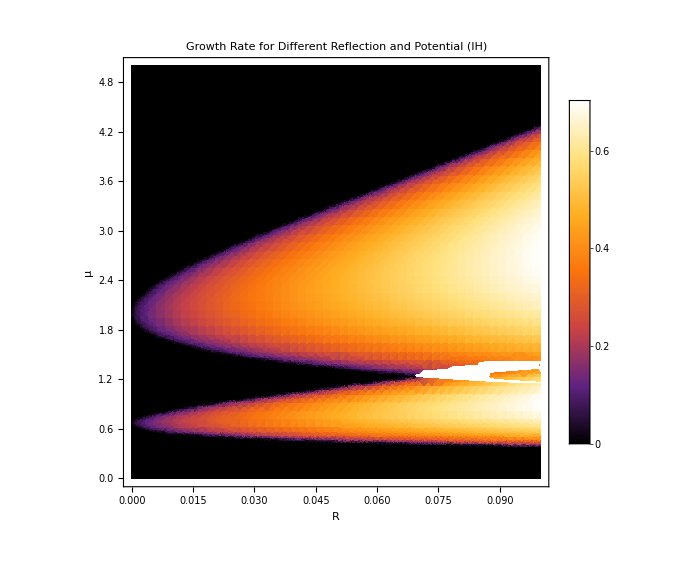

```mathematica
DensityPlot[
MaxEV[IDLConstructor[thetaList,{1,1,-reflection,-reflection}*mu,omegaVList,varList],varList],
{reflection,0,0.1},{mu,0,5},PlotLegends->Automatic,FrameLabel->{"R","μ"},ColorFunction->"SunsetColors",PlotLabel->"Growth Rate for Different Reflection and Potential (IH)",ImageSize->Large,PlotPoints->50
]
```